```mathematica
Quit[]
```

# functions

```mathematica
(* -------------------------------------------- Smoothed power spectrum ----------------------------------------------------*)

(* functions for two peaks' locations *)
x1stpk[β_]:=1.69-0.362β+0.0326 β^2;
x2ndpk[β_]:=2.14-0.145β-0.406 β^2-0.235 β^3-0.0465 β^4;
(* functions for two peaks' amplitudes *)
f1[β_]:=1637.551+2376.283 β+1310.923 β^2+323.051 β^3+29.949 β^4;
f2[β_]:=51.354+89.605β+60.791 β^2+18.264 β^3+2.086 β^4;
(* solve beta (half of second slow-roll parameter in CR phase) *)
solvebeta[ratk_,ratP_]:=FindRoot[ratP==(ratk*x1stpk[β]/x2ndpk[β])^(2β+6)*f2[β]/f1[β],{β,-2.5}][[1]][[2]];
(* solve NCR (duration of CR phase) *)
solveNCR[ratk_,ratP_]:=Log[ratk x1stpk[solvebeta[ratk,ratP]]/x2ndpk[solvebeta[ratk,ratP]]];
(* breakpoints of the piecewise function for smoothed power spectrum *)
kcut1[k1_,τs_]:=k1-π/(2τs);
kcut2[k2_,τe_]:=k2-π/(2τe);
ν[β_]:=Abs[3/2+β];
kmid[β_,τe_]:=-((3-2ν[β])/(2ν[β]-1)*d0[β]/d2[β])^(1/2)*1/τe;
(* functions for the power spectrum around first peak,if beta<-3/2 *)

𝒲d[β_]:=540 (8 β^2)^-1(-9+2 β) (-7+2 β) (-5+2 β) (9-40 β^2+16 β^4)^2 ;
𝒲0[β_]:=120 β^2 (-9+2 β) (-7+2 β) (-5+2 β) (3+4 (-2+β) β)^2
𝒲2[β_]:=30 (-9+2 β)(-7+2 β)(-5+2 β)(3-2 β)^2   (-1+2 β) (-1-2 β+4 β^2);
𝒲4[β_]:=60 β (-9+2 β) (-7+2 β) (-5+2 β) (-3+2 β) (1+2 (-2+β) β);
𝒲6[β_]:=10 β (-9+2 β) (-7+2 β) (-3+2 β) (9+2 β (-7+2 β));
𝒲8[β_]:=20 (-2+β) β (-9+2 β) (5+(-5+β) β);
𝒲10[β_]:=(-3+β) β (35-26 β+4 β^2);
𝒲12[β_]:=(648 β-762 β^2+326 β^3-60 β^4+4 β^5)/(3 (-11+2 β) (-5+2 β));
𝒲14[β_]:=(1540 β-1453 β^2+499 β^3-74 β^4+4 β^5)/(21 (-13+2 β) (-11+2 β) (-5+2 β));

(* smoothed power spectrum around first peak *)

Psmo1stpk[k_,β_,AIR_,τs_,τe_]:=AIR*(τe/τs)^(4β+6)(-k*τs)^4 1/𝒲d[β](𝒲0[β]+𝒲2[β]*(-k*τs)^2+𝒲4[β]*(-k*τs)^4+𝒲6[β]*(-k*τs)^6+𝒲8[β]*(-k*τs)^8+𝒲10[β]*(-k*τs)^10+𝒲12[β]*(-k*τs)^12+𝒲14[β]*(-k*τs)^14);

(* functions for the power spectrum around second peak *)

d0[β_]:=1+(4 β)/3-(19 β^2)/72-(103 β^3)/72-(413 β^4)/288-(61 β^5)/72-(43 β^6)/144-β^7/18-β^8/288;
d2[β_]:=β/2880*(-3072+196β+836 β^2+713 β^3+360 β^4+114 β^5+20 β^6+β^7);
d4[β_]:=β/50400*(11520-364β-1404 β^2-1093 β^3-492 β^4-142 β^5-24 β^6-β^7);
d6[β_]:=β/(50400*27)*(-30720+580β+2116 β^2+1553 β^3+640 β^4+170 β^5+28 β^6+β^7);
d8[β_]:=β/52390800*(67200-844β-2972 β^2-2093 β^3-804 β^4-198 β^5-32 β^6-β^7);
d10[β_]:=β/50400^2*(-129024+1156β+3972 β^2+2713 β^3+984 β^4+226 β^5+36 β^6+β^7);
d12[β_]:=β/183891708000*(225792-1516β-5116 β^2-3413 β^3-1180 β^4-254 β^5-40 β^6-β^7);

(* smoothed power spectrum on Ultraviolet limit *)

AUV[β_,AIR_,τs_,τe_]:=AIR*(τe/τs)^(2 β);

(* smoothed power spectrum around second peak *)

Psmo2ndpk[k_,β_,AIR_,τs_,τe_]:=AUV[β,AIR,τs,τe]*(d0[β]+d2[β]*(-k τe)^2+d4[β]*(-k τe)^4+d6[β]*(-k τe)^6+d8[β]*(-k τe)^8+d10[β]*(-k τe)^10+d12[β]*(-k τe)^12);

(* functions for power spectrum between first peak and second peak *)

Amid[β_,AIR_,τs_,τe_]:=AUV[β,AIR,τs,τe]*(d0[β]+d2[β]*(-kmid[β,τe] τe)^2);
δ[β_]:=If[-2<β⩽-3/2,-0.63-1.44(β+3/2)-0.43(β+3/2)^2,If[-3/2<β<-1,-0.63+2.5(β+3/2)-2.9(β+3/2)^2,0]];
(* smoothed power spectrum between first peak and second peak *)
Pmid[k_,β_,AIR_,τs_,τe_]:=Amid[β,AIR,τs,τe]*(k/kmid[β,τe])^(3-2ν[β]+δ[β]);

(* smoothed power spectrum *)

Psmol4[k_,β_,AIR_,τs_,τe_,k1_,k2_]:=Psmo1stpk[k,β,AIR,τs,τe]*UnitStep[kcut1[k1,τs]-k]+Pmid[k,β,AIR,τs,τe]*UnitStep[k-kcut1[k1,τs]]*UnitStep[kmid[β,τe]-k]+Psmo2ndpk[k,β,AIR,τs,τe]*UnitStep[k-kmid[β,τe]]*UnitStep[kcut2[k2,τe]-k]+AUV[β,AIR,τs,τe]*UnitStep[k-kcut2[k2,τe]];
Psmol3[k_,β_,AIR_,τs_,τe_,k1_,k2_]:=Psmo1stpk[k,β,AIR,τs,τe]*UnitStep[kcut1[k1,τs]-k]+Psmo2ndpk[k,β,AIR,τs,τe]*UnitStep[k-kcut1[k1,τs]]*UnitStep[kcut2[k2,τe]-k]+AUV[β,AIR,τs,τe]*UnitStep[k-kcut2[k2,τe]];
Psmo[k_,β_,AIR_,τs_,τe_,k1_,k2_]:=If[kmid[β,τe]<kcut1[k1,τs],Psmol3[k,β,AIR,τs,τe,k1,k2],Psmol4[k,β,AIR,τs,τe,k1,k2]];

(* -------------------------------------------- Exact power spectrum ----------------------------------------------------*)

C2[β_,k_,τs_]:=(π ⅇ^(-ⅈ k τs))/(2^(7/2) √k (-k τs)^(3/2)) (2 k τs (1+ⅈ k τs) HankelH2[-1+ν[β],-k τs]-((3+2 β-2 ν[β])(1+ⅈ k τs)-2 k^2 τs^2) HankelH2[ν[β],-k τs]);
D2[β_,k_,τs_]:=-(π ⅇ^(-ⅈ k τs))/(2^(7/2) √k (-k τs)^(3/2))  (2 k τs (1+ⅈ k τs) HankelH1[-1+ν[β],-k τs]-((3+2 β-2 ν[β])(1+ⅈ k τs)-2 k^2 τs^2) HankelH1[ν[β],-k τs]);
A[β_,k_,τs_,τe_]:=(ⅇ^(ⅈ k τe)√k)/(2^(3/2)  (-k τe)^(3/2))(C2[β,k,τs] ((2k τe (1-ⅈ k τe)) HankelH1[-1+ν[β],-k τe]+((3+2 β-2 ν[β]) (-1+ⅈ k τe)+2 k^2 (τe)^2) HankelH1[ν[β],-k τe])+ D2[β,k,τs]( (2k τe (1-ⅈ k τe)) HankelH2[-1+ν[β],-k τe]+((3+2 β-2 ν[β])(-1+ⅈ k τe)+2 k^2 (τe)^2) HankelH2[ν[β],-k τe]));
B[β_,k_,τs_,τe_]:=(ⅇ^(-ⅈ k τe)√k)/(2^(3/2)  (-k τe)^(3/2))(C2[β,k,τs] ((2k τe (1+ⅈ k τe)) HankelH1[-1+ν[β],-k τe]+((3+2 β-2 ν[β]) (-1-ⅈ k τe)+2 k^2 (τe)^2) HankelH1[ν[β],-k τe])+ D2[β,k,τs]( (2k τe (1+ⅈ k τe)) HankelH2[-1+ν[β],-k τe]+((3+2 β-2 ν[β])(-1-ⅈ k τe)+2 k^2 (τe)^2) HankelH2[ν[β],-k τe]));
PRexa[k_,β_,AIR_,τs_,τe_]:=AUV[β,AIR,τs,τe]*(Abs[A[β,k,τs,τe]-B[β,k,τs,τe]])^2;

(* -------------------------------------------- Transfer function in GW ----------------------------------------------------*)

T[s_,t_]:=(288*(-5+s^2+t(2+t))^2)/((1-s+t)^6*(1+s+t)^6)*(π^2/4*(-5+s^2+t(2+t))^2*UnitStep[t-(Sqrt[3]-1)]+(-(t-s+1)(t+s+1)+1/2(-5+s^2+t(2+t))*Log[Abs[(-2+t(2+t))/(3-s^2)]])^2);
```

# Input

```mathematica
(* Wavenumber of the first peak in the curvature perturbation power spectrum *)
k1stpk=1; 
(* Ratio of the second peak wavenumber to the first peak wavenumber, should be larger than 10^0.7*)
k2k1=10;
(* Ratio of the second peak wavenumber to the first peak amplitude, should be larger than 10^-0.25*)
(* The input values of k2k1 and A2A1 should satiesfy log10[A2A1] ≤ -0.727 + 2.015 log10[k2k1] *)
A2A1=10;
(* Power spectrum amplitude around the CMB scale (infrared normalization) *)
AIR=2*10^-9;
```

# Solve (β,N_CR) from (k_(2ndpk)/k_(1stpk), A_(2ndpk)/A_(1stpk))

```mathematica
(* Wavenumber of the second peak in the curvature perturbation power spectrum *)
k2ndpk=k1stpk*k2k1;

(* beta:Half of the second slow-roll parameter. Should be between-3 and-2, values outside this range are considered unreliable as solutions. *)
β=Round[solvebeta[k2k1,A2A1],10^-4]//N
(* NCR:Duration of the constant-roll stage. *)
NCR=solveNCR[k2k1,A2A1]

(* Time of the SR-CR transition *)
τs=-x1stpk[β]/k1stpk
(* -1/tau_s *)
kstar=-1/τs
(* Time of the CR-SR transition *)
τe=-x2ndpk[β]/k2ndpk

(*κs=-k τs =k/kstar*)
κslist=Table[10^x,{x,Log10[(k1stpk*10^-1)/kstar],Log10[(k2ndpk*10^1.5)/kstar],(Log10[(k2ndpk*10^1.5)/kstar]-Log10[(k1stpk*10^-1)/kstar])/150}]; (*f=1.5*10^-15*k;*)
```

-2.2535

2.64587

-2.67132

0.374347

-0.189511

# Power Spectra

LogLogPlot::precw: 参数函数的精度 ({0.000301981 Abs[11.4479 Power[«2»] Plus[«2»]-11.4479 Power[«2»] Plus[«2»]]^2-0,1. ⅇ^(Charting`Private`pvar$8516)-0,0.070943 ⅇ^(Charting`Private`pvar$8516)-0,ⅇ^(Charting`Private`pvar$8516)-0,1. Im[ⅇ^(Charting`Private`pvar$8516)]-0,0.070943 Im[ⅇ^(Charting`Private`pvar$8516)]-0}) 小于 WorkingPrecision (50.).

LogLogPlot::precw: 参数函数的精度 ({True,True,True,True,1. Re[ⅇ^(Charting`Private`pvar$8516)]≤0,0.070943 Re[ⅇ^(Charting`Private`pvar$8516)]≤0}) 小于 WorkingPrecision (50.).

LogLogPlot::precw: 参数函数的精度 ({«1»}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，LogLogPlot::precw 的进一步输出将被抑制.

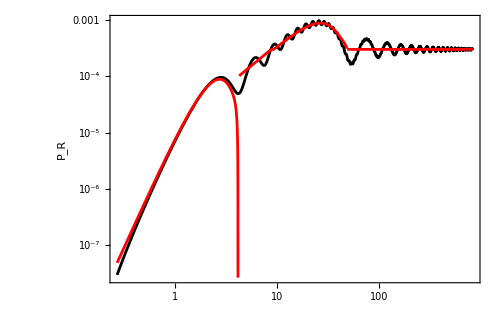

```mathematica
LogLogPlot[{PRexa[κs*kstar,β,AIR,τs,τe],Psmo[κs*kstar,β,AIR,τs,τe,k1stpk,k2ndpk]},{κs,(k1stpk*10^-1)/kstar,(k2ndpk*10^1.5)/kstar},PlotRange->All,Frame->True,PlotStyle->{Black,Red},GridLines->{{1,-k1stpk*τs,-k2ndpk*τs},{AIR,AUV[β,AIR,τs,τe]}},WorkingPrecision->50,LabelStyle->{FontSize->20,FontFamily->"Times New Roman",Black},FrameLabel->{Style["",FontFamily->"Times",FontSize->20],Style["P_R",FontFamily->"Felipa",FontSize->20]Style["",FontFamily->"Times",FontSize->20]},ImageSize->500,PlotLegends->Placed[Framed[LineLegend[{Black,Red},{"Exact","Smoothed"},LegendMarkerSize->20,LegendLayout->{"Column",1},LabelStyle->{FontFamily->"Times New Roman",FontSize->15,Black}],RoundingRadius->10,FrameStyle->Black,Background->None],{0.8,0.26}]]
```

# IGW-smoothed

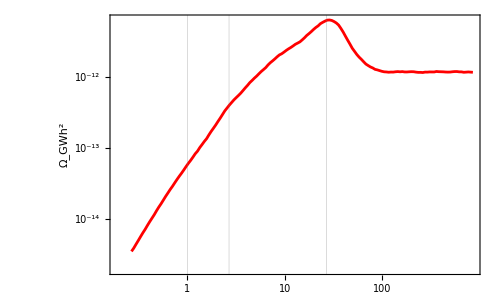

```mathematica
ΩGWrsmo=NIntegrate[1/12*((t(2+t)(s^2-1))/((1-s+t)(1+s+t)))^2*T[s,t]*Psmo[(s+t+1)/2*#*kstar,β,AIR,τs,τe,k1stpk,k2ndpk]*Psmo[(t-s+1)/2*#*kstar,β,AIR,τs,τe,k1stpk,k2ndpk],{t,0,Infinity},{s,-1,1},Method->"AdaptiveMonteCarlo",WorkingPrecision->10]&/@κslist;
ΩGW0smo=1.6*10^-5*ΩGWrsmo;

plotΩGW0smo=ListLogLogPlot[Transpose[{κslist,GaussianFilter[ΩGW0smo,1.5]}],Joined->True,Frame->True,PlotStyle->Red,FrameLabel->{Row[{Style["",Italic]}],"Ω_GWh^2"},GridLines->{{1,-k1stpk*τs,-k2ndpk*τs},None},LabelStyle->{FontSize->20,FontFamily->"Times New Roman",Black},LabelStyle->{FontSize->20,FontFamily->"Times New Roman",Black},ImageSize->500,AspectRatio->3/5]
```

# IGW-exact

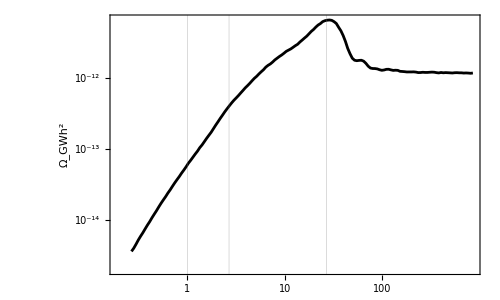

```mathematica
ΩGWrexa=NIntegrate[1/12*((t(2+t)(s^2-1))/((1-s+t)(1+s+t)))^2*T[s,t]*PRexa[(s+t+1)/2*#*kstar,β,AIR,τs,τe]*PRexa[(t-s+1)/2*#*kstar,β,AIR,τs,τe],{t,0,Infinity},{s,-1,1},Method->"AdaptiveMonteCarlo",WorkingPrecision->10]&/@κslist;
ΩGW0exa=1.6*10^-5*ΩGWrexa;

plotΩGW0exa=ListLogLogPlot[Transpose[{κslist,GaussianFilter[ΩGW0exa,1.5]}],Joined->True,Frame->True,PlotStyle->Black,GridLines->{{1,-k1stpk*τs,-k2ndpk*τs},None},FrameLabel->{Row[{Style["",Italic]}],"Ω_GWh^2"},LabelStyle->{FontSize->20,FontFamily->"Times New Roman",Black},LabelStyle->{FontSize->20,FontFamily->"Times New Roman",Black},ImageSize->500,AspectRatio->3/5,AspectRatio->3/5]
```

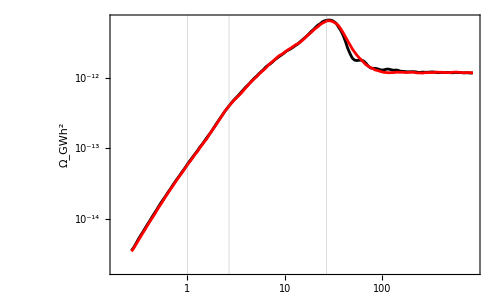

```mathematica
ListLogLogPlot[{Transpose[{κslist,GaussianFilter[ΩGW0exa,1.5]}],Transpose[{κslist,GaussianFilter[ΩGW0smo,1.5]}]},Joined->True,Frame->True,PlotStyle->{Black,Red},FrameLabel->{Row[{Style["",Italic]}],"Ω_GWh^2"},GridLines->{{1,-k1stpk*τs,-k2ndpk*τs},None},LabelStyle->{FontSize->20,FontFamily->"Times New Roman",Black},LabelStyle->{FontSize->20,FontFamily->"Times New Roman",Black},ImageSize->500,PlotLegends->Placed[Framed[LineLegend[{Black,Red},{"Exact","Smoothed"},LegendMarkerSize->20,LegendLayout->{"Column",1},LabelStyle->{FontFamily->"Times New Roman",FontSize->15,Black}],RoundingRadius->10,FrameStyle->Black,Background->None],{0.8,0.26}],AspectRatio->3/5]
```